### Mass Matrix - 1 Flavour Scenario for Both Sided Completely Non-local Clockwork

```mathematica
K = 7;r=1.2;a=1;q=4.0;
(* qt is q^∼ (Majorana mass term), K is the number of sites and a is mass term (m) and q is Dirac mass term in cw fermions and r is the decaying factor. *)
```

```mathematica
Ox = Table[0,{x,K},{y,K+1}];
```

```mathematica
i=1;While[i<K+1,{Ox[[i,i]] = a};i++]
j=1;
While[j<K+1,{i=1;While[i<K+1-j+1,{Ox[[i,j+1+i-1]] = -q/r^(j-1)};i++]};j++]
j=1;
While[j<K,{i=1;While[i<K+1-j,{Ox[[j+i,i]] = -q/r^(j-1)};i++]};j++]
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
Ox
```

(1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | -1.60751 | -1.33959
-4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | -1.60751
-3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901
-2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481
-2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778
-1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333
-1.60751 | -1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4.)

```mathematica
Rw = Transpose[Ox].Ox
```

(47.4907 | 28.5888 | 37.24 | 41.2657 | 41.7781 | 39.6091 | 35.3652 | 37.2407
28.5888 | 60.9066 | 38.8213 | 44.63 | 46.0597 | 44.1358 | 39.6091 | 42.3311
37.24 | 38.8213 | 68.2966 | 43.6152 | 46.9877 | 46.0597 | 41.7781 | 46.0034
41.2657 | 44.63 | 43.6152 | 70.6543 | 43.6152 | 44.63 | 41.2657 | 47.814
41.7781 | 46.0597 | 46.9877 | 43.6152 | 68.2966 | 38.8213 | 37.24 | 47.1444
39.6091 | 44.1358 | 46.0597 | 44.63 | 38.8213 | 60.9066 | 28.5888 | 43.1574
35.3652 | 39.6091 | 41.7781 | 41.2657 | 37.24 | 28.5888 | 47.4907 | 34.7423
37.2407 | 42.3311 | 46.0034 | 47.814 | 47.1444 | 43.1574 | 34.7423 | 48.2852)

```mathematica
Eigenvalues[Rw]
```

{347.992,28.5365,27.7509,26.0696,22.5837,15.0575,4.33692,-1.5099×10^-14}

```mathematica
Eigenvectors[Rw]
```

(-0.312387 | -0.351711 | -0.376547 | -0.385558 | -0.3778 | -0.352655 | -0.309707 | -0.353913
0.12795 | -0.331353 | 0.478544 | -0.527954 | 0.481637 | -0.340368 | 0.134753 | -0.0105411
-0.241064 | 0.521425 | -0.409572 | 0.0132093 | 0.402622 | -0.520461 | 0.26174 | -0.0242576
0.358778 | -0.459427 | -0.107639 | 0.532073 | -0.145157 | -0.450909 | 0.372701 | -0.047126
0.415981 | -0.226005 | -0.523201 | 0.0164722 | 0.510523 | 0.154044 | -0.456203 | 0.0968865
0.526406 | 0.186521 | -0.280005 | -0.465967 | -0.216972 | 0.233624 | 0.472874 | -0.259443
0.0601141 | -0.0195687 | -0.152412 | -0.266745 | -0.289818 | -0.184081 | 0.0310861 | 0.884745
-0.495431 | -0.44418 | -0.272949 | -0.0279901 | 0.224529 | 0.4164 | 0.495794 | 0.111145)

```mathematica
zr = Table[0,{i,1,K},{j,1,K}];
zr1 = Table[0,{i,1,K+1},{j,1,K+1}];
```

```mathematica
Mt = ArrayFlatten[{{zr,Ox},{Transpose[Ox],zr1}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | -1.60751 | -1.33959
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | -1.60751
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.60751 | -1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4.
1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | -1.60751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | -1.92901 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | -2.31481 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | -2.77778 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | -3.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.60751 | -1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.33959 | -1.60751 | -1.92901 | -2.31481 | -2.77778 | -3.33333 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ev = Eigenvalues[Mt]
```

{-18.6545,18.6545,-5.34196,5.34196,-5.26791,5.26791,5.10584,-5.10584,-4.75223,4.75223,-3.8804,3.8804,2.08253,-2.08253,4.05318×10^-16}

```mathematica
Y = Eigenvectors[Mt];
```

```mathematica
H= Inverse[Y];
```

```mathematica
Ev1 = Sort[Abs[ ev]];
```

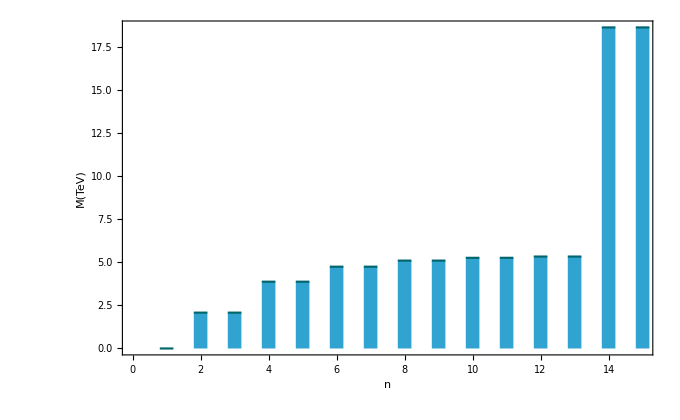

```mathematica
DiscretePlot[Ev1⟦i⟧,{i,1,2 K+1},PlotStyle->Directive[RGBColor[0.,0.4,0.42],Opacity[1.],AbsoluteThickness[1.545]],ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,0.6,0.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"n","M(TeV)"},LabelStyle->Directive[Bold,Medium],PlotRange->{0,All}, Epilog->{Text[ "",Scaled[{0.8,0.95}]],Text["",Scaled[{0.8,0.9}]]}]
```

```mathematica
Rn = H[[2K+1,All]] 
(* Change of basis from Subscript[ψ^c, R,r]  to eigenvector of cw2 in interaction term. *)
```

{-0.250254,-0.250254,-0.00745367,0.00745367,0.0171527,-0.0171527,0.0333231,-0.0333231,0.0685091,-0.0685091,-0.183454,0.183454,0.625609,-0.625609,-0.111145}

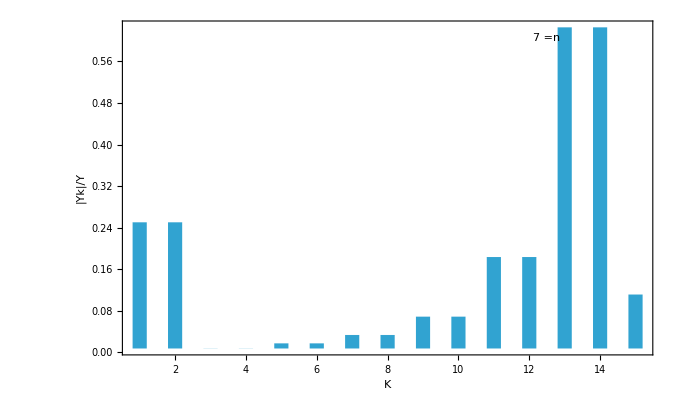

```mathematica
DiscretePlot[Abs[Rn[[i]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],PlotRange->All,Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```